```mathematica
(*1*)
h[t_,u_]:=20Sin[u];
RK3[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;

For[i=2, i≤n,i++,
k1 = h*du[t+i*h, y[[i-1]]]//N;
k2 = h*du[t+i*h+1/3 h, y[[i-1]]+1/3 k1]//N;
k3=h*du[t+i*h+2/3 h, y[[i-1]]+2/3 k2]//N;
y[[i]]=y[[i-1]]+(1/4 k1+3/4 k3)//N; 
];

ret = Table[{t+(i-1)*h, y[[i]]}, {i,1,n}]
]
```

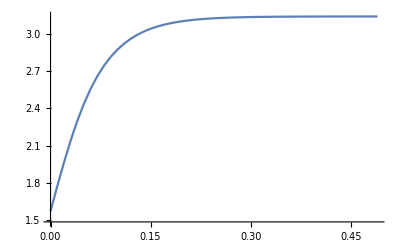

```mathematica
ListLinePlot[RK3[h, Pi/2, 0,1/2, 0.01], PlotRange->All]
```

```mathematica
(*2*)
RK4[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3,k4},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;

For[i=2, i≤n,i++,
k1 = h*du[t+i*h, y[[i-1]]]//N;
k2 = h*du[t+i*h+1/2 h, y[[i-1]]+1/2 k1]//N;
k3=h*du[t+i*h+1/2 h, y[[i-1]]+1/2 k2]//N;
k4 = h*du[t+i*h+2/3 h,y[[i-1]]+k3]//N;
y[[i]]=y[[i-1]]+(1/6 k1+1/3 k2+1/3 k3+1/6 k4)//N; 
];

ret = Table[{t+(i-1)*h, y[[i]]}, {i,1,n}]
]
```

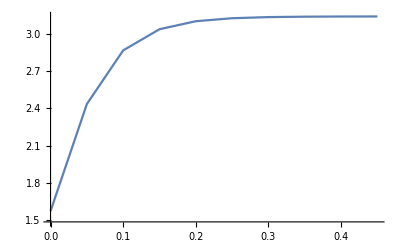

```mathematica
ListLinePlot[RK4[h, Pi/2, 0,1/2, 0.05], PlotRange->All]
```

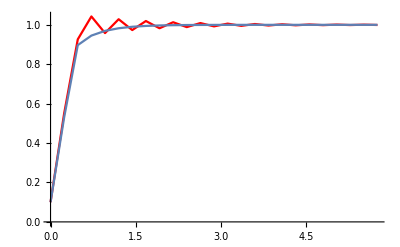
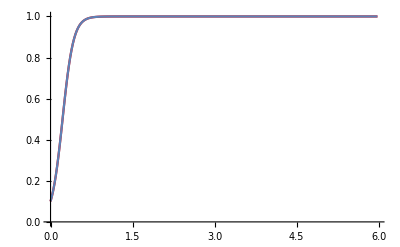

```mathematica
(*3*)
g[t_,u_]:=10u(1-u);
l = {6/25,6/250};
Table[
Show[{
ListLinePlot[RK3[g, 0.1, 0,6, l[[i]]], PlotRange->All, PlotStyle->Red],
ListLinePlot[RK4[g,0.1, 0,6, l[[i]]], PlotRange->All]
}
],
{i,1,2}
]
```

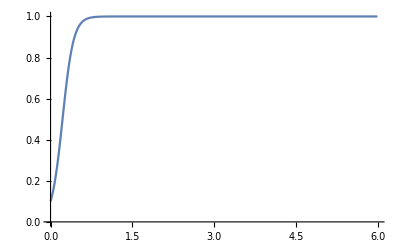

```mathematica
ListLinePlot[RK4[g,0.1, 0,6, 6/400], PlotRange->All]
```

```mathematica
(*4*)
```

```mathematica
alpha[du_,du0_, t_,T_, h_, metod_]:=Module[
{res},
l = {1,2,4};
res = Table[metod[du,du0, t,T, h/l[[i]]],{i,1,3}];
(*Print[res[[1]][[1,2]]];*)

ret = Table[{res[[1]][[i,1]],Log[Abs[(res[[1]][[i,2]]-res[[2]][[1+2(i-1),2]])/(res[[2]][[1+2(i-1),2]]-res[[3]][[1+4(i-1),2]])]]/Log[2]}//N,{i,1,Length[res[[1]]]}]
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

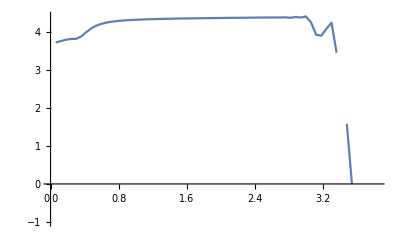

```mathematica
ListLinePlot[alpha[g, 0.1, 0,6, 6/100, RK4], PlotRange->All]
```

```mathematica
b[t_]:=Piecewise[{{1, 0≤t≤2}, {3, t>2}}]
r[t_,u_]:=-b[t]*u+t;
a[t_]:=Piecewise[{{t-1+2 E^-t, 0≤t≤2}, {1/3 t-1/9+E^(-3t)(4/9 E^6+2 E^4), t>2}}]
```

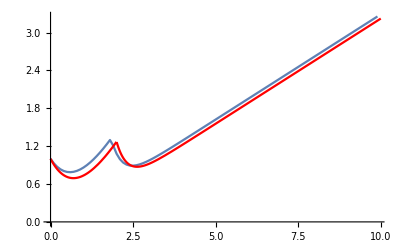

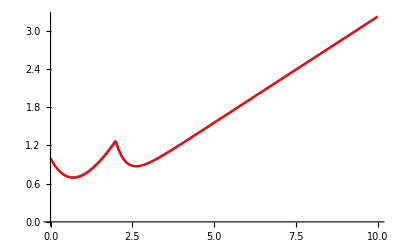

```mathematica
Show[{
ListLinePlot[RK3[r,1,0,10,0.1]],
Plot[a[t],{t,0,10},PlotStyle->Red]
}]
Show[{
ListLinePlot[RK3[r,1,0,10,0.01]],
Plot[a[t],{t,0,10},PlotStyle->Red]
}]
```